```mathematica
(*for mu=(nn+1)wc*)
mmp
```

{{1,-6.×10^-6},{2,-0.0000495553},{3,-0.000167862},{4,-0.000405143},{5,-0.000797594},{6,-0.00138508},{7,-0.00220689},{8,-0.00330234},{9,-0.00471073},{10,-0.00647138},{11,-0.00862359},{12,-0.0112067},{13,-0.0142599},{14,-0.0178227},{15,-0.0219342},{16,-0.0266339},{17,-0.0319609},{18,-0.0379547},{19,-0.0446545},{20,-0.0520996},{21,-0.0603294},{22,-0.0693831},{23,-0.0793001},{24,-0.0901197},{25,-0.101881},{26,-0.114624},{27,-0.128387},{28,-0.14321},{29,-0.159132},{30,-0.176192},{31,-0.19443},{32,-0.213887},{33,-0.2346},{34,-0.256611},{35,-0.279906},{36,-0.30464},{37,-0.330775},{38,-0.35831},{39,-0.38738},{40,-0.418368},{41,-0.450157},{42,-0.409847},{43,-0.519342},{44,-0.556917},{45,-0.595106},{46,-0.636133}}

```mathematica
(*for mu=(nn+5/4)wc*)
mmp
```

{{1,-0.0000117187},{2,-0.0000695119},{3,-0.000214604},{4,-0.000486704},{5,-0.000924138},{6,-0.00156642},{7,-0.00245286},{8,-0.00362276},{9,-0.00511544},{10,-0.0069702},{11,-0.00922635},{12,-0.0119232},{13,-0.0151},{14,-0.0187962},{15,-0.023051},{16,-0.0279037},{17,-0.0333937},{18,-0.0395602},{19,-0.0464425},{20,-0.0540801},{21,-0.062512},{22,-0.0717778},{23,-0.0819166},{24,-0.0929679},{25,-0.104971},{26,-0.117965},{27,-0.131989},{28,-0.147083},{29,-0.163286},{30,-0.180637},{31,-0.199176},{32,-0.218942},{33,-0.239976},{34,-0.262317},{35,-0.28595},{36,-0.31104},{37,-0.33753},{38,-0.365433},{39,-0.39488},{40,-0.426073},{41,-0.458354},{42,-0.463942},{43,-0.528447},{44,-0.567506},{45,-0.605209},{46,-0.64891}}

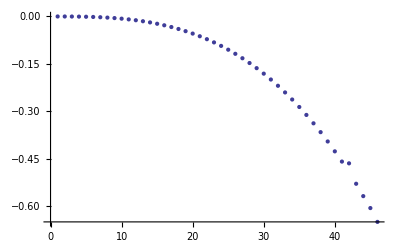

```mathematica
ListPlot[mmp,PlotRange->Automatic]
```

```mathematica
mmpline=Fit[mmp,{x^3,x^4},x] (* nn+1 *)
```

-6.59328×10^-6 x^3+3.51865×10^-9 x^4

```mathematica
mmpline=Fit[mmp,{x^3,x^4},x] (* nn+5/4 *)
```

-6.79278×10^-6 x^3+4.03448×10^-9 x^4

```mathematica
mmpline=Fit[mmp,{x^3},x]
```

-6.66891×10^-6 x^3

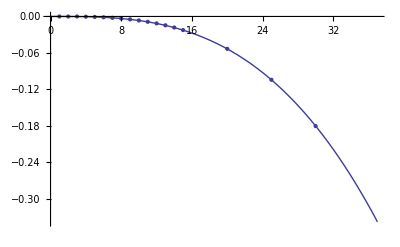

```mathematica
Show[Plot[mmpline,{x,0,37},PlotRange->Automatic],ListPlot[mmp]]
```